```mathematica
M={{6,5,4},{5,10,1},{4,1,5}};
```

```mathematica
M//MatrixForm
```

(6 | 5 | 4
5 | 10 | 1
4 | 1 | 5)

```mathematica
Eigenvalues[M]//N
```

{14.4547,5.97823,0.56704}

```mathematica
M={{1,1},{2,0}};
Eigenvalues[%]//N
```

{2.,-1.}

```mathematica
t=GoldenRatio//N
a=(Cos[Pi/10]+I Sin[Pi/10])//N
b=(Cos[2 Pi/5]+I Sin[2 Pi/5])//N
c=(Cos[Pi/5]+I Sin[Pi/5])//N
d=Sqrt[2+t]
```

1.61803

0.951057+0.309017 ⅈ

0.309017+0.951057 ⅈ

0.809017+0.587785 ⅈ

1.90211

```mathematica
thick={0.,1.5,1.5+1.5 b,1.5 b,1}
thin={0,1.5,1.5+1.5 c,1.5 c,-1}
```

{0.,1.5,1.96353+1.42658 ⅈ,0.463525+1.42658 ⅈ,1}

{0,1.5,2.71353+0.881678 ⅈ,1.21353+0.881678 ⅈ,-1}

```mathematica
dissect[{p_,q_,r_,s_,-1}]:=Block[{w,y,z,u},
w=p+((1/d) (q-p)) Conjugate[a];
y=p+((1/d) (s-p)) a;
z=w+y-p;
u=z+s-y;
{{z,y,p,w,1 },{w,q,u,z,-1},{u,s,y,z,-1}}]
```

```mathematica
dissect[{p_,q_,r_,s_,1}]:=Block[{w,y,z,u,v},
w=p+(1/d) (q-p) Conjugate[a];
y=p+(1/d) (s-p) Conjugate[a];
z=w+y-p;
u=z+s-y;
v=q+z-w;
{{z,y,p,w,1},{z,u,s,y,1},{z,v,r,u,1},{w,q,v,z,-1}}
]
```

```mathematica
dissect[list_]:=Map[dissect,list]
```

```mathematica
Config[n_]:=(tiles=Nest[dissect,thin,n]/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}]
Show[Graphics[tiles],AspectRatio->Automatic,PlotRange->All])
```

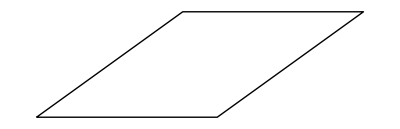

```mathematica
Nest[dissect,thin,0];
%/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}];
Graphics[%]
```

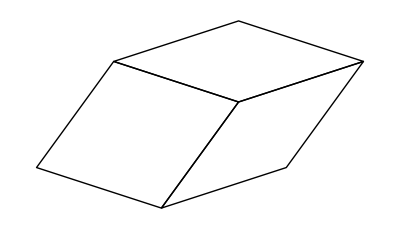

```mathematica
Nest[dissect,thin,1];
%/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}];
Graphics[%]
```

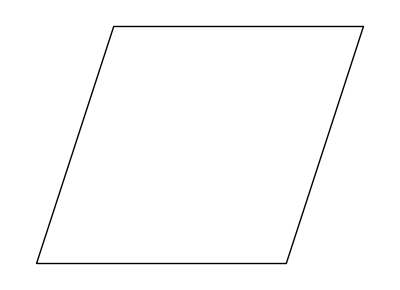

```mathematica
Nest[dissect,thick,0];
%/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}];
Graphics[%]
```

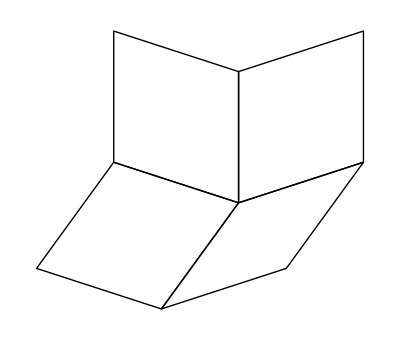

```mathematica
Nest[dissect,thick,1];
%/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}];
Graphics[%]
```

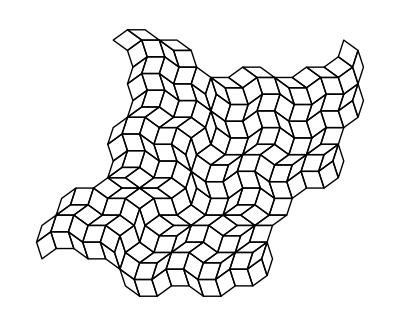

/home/nicolas/git/talks/2017 PhD Defense/img/4_part3/thick_4.pdf

```mathematica
n=4;
Nest[dissect,thick,n];
%/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}];
Graphics[%]
Export[NotebookDirectory[]<>"thick_"<>ToString[n]<>".pdf",%]
```

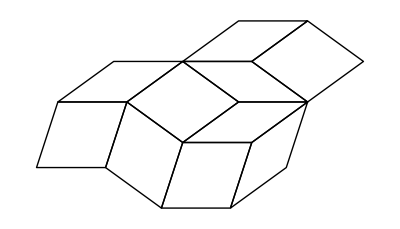

/home/nicolas/git/talks/2017 PhD Defense/img/4_part3/thin_2.pdf

```mathematica
n=2;
Nest[dissect,thin,n];
%/.{p_,q_,r_,s_,x_}->Line[{{Re[p],Im[p]},{Re[q],Im[q]},{Re[r],Im[r]},{Re[s],Im[s]},{Re[p],Im[p]}}];
Graphics[%]
Export[NotebookDirectory[]<>"thin_"<>ToString[n]<>".pdf",%]
```